```mathematica
α2 = Table[Integrate[Cos[(m π)/L y]Sin[(n π)/(2L)y]Sin[π/(2L)y],{y,-L,0}],{m,0,5},{n,1,5}];
α2f = Table[Integrate[Cos[(m π)/L y]Sin[(n π)/(2L)y]Sin[π/(2L)y],{y,0,L}],{m,0,1},{n,1,1}];
α1 = Table[Integrate[Cos[(m π)/L y]Cos[π/L y]Sin[(n π)/(2L)y],{y,-L,0}],{m,0,5},{n,1,5}];
```

```mathematica
Total[Total[α1]]
```

-(2050546 L)/(765765 π)

{{0,0,0,0,0},{0,0,0,0,0},{(52 L)/(105 π),(52 L)/(105 π),(52 L)/(105 π),(52 L)/(105 π),(52 L)/(105 π)},{(2 L)/(5 π),(2 L)/(5 π),(2 L)/(5 π),(2 L)/(5 π),(2 L)/(5 π)},{(392 L)/(2145 π),(392 L)/(2145 π),(392 L)/(2145 π),(392 L)/(2145 π),(392 L)/(2145 π)},{(2 L)/(21 π),(2 L)/(21 π),(2 L)/(21 π),(2 L)/(21 π),(2 L)/(21 π)}}

```mathematica
a0func[n_, m_]:= If[n!= 2m,-(2 L (n))/((-4 m^2+n^2) π),0]
```

```mathematica
a2func[n_, m_ ]:= If[n ==2m -1, -L/4, If[n== 2m +1, L/4, If[n==-1-2m, -L/4, If[n ==1-2m, L/4, (L ((2 (2 m-n) Cos[m π-(n π)/2])/(-1+(-2 m+n)^2)-(2 (2 m+n) Cos[m π+(n π)/2])/(-1+4 m^2+4 m n+n^2)))/(2 π)]]]]
```

```mathematica
a2func[11,6]
```

-L/4

```mathematica
Integrate[Cos[6 π/L y]Sin[π y/(2L)]Sin[11 π/(2L)y],{y,-L, 0}]
```

-L/4

```mathematica
a0func[1,3]
```

(2 L)/(35 π)

```mathematica
2L (-1)/(π(1-4*9))
```

(2 L)/(35 π)

```mathematica
Integrate
```

L^2/(35 π)

```mathematica
(*MatrixForm[α2+α2f]*)
```

```mathematica
FullSimplify[Integrate[Cos[(m π)/L y]Sin[((-1-2m) π)/(2L)y]Sin[π/(2L)y],{y,-L,0}]]
FullSimplify[Integrate[Cos[(m π)/L y]Sin[((1-2m) π)/(2L)y]Sin[π/(2L)y],{y,-L,0}]]
```

```mathematica
TeXForm[1/8 L (-2-((1+4 m) Sin[2 m π])/(m (1+2 m) π))/.m->2]
```

-\frac{L}{4}

```mathematica
TeXForm[1/8 L (2+((1+4 m) Sin[2 m π])/(m (1+2 m) π))]
```

\frac{1}{8} L \left(\frac{(4 m+1) \sin (2 \pi  m)}{\pi  m (2 m+1)}+2\right)

```mathematica
TeXForm[1/8 L (-2+((1-4 m) Sin[2 m π])/(m (-1+2 m) π))]
```

\frac{1}{8} L \left(\frac{(1-4 m) \sin (2 \pi  m)}{\pi  m (2 m-1)}-2\right)

```mathematica
TeXForm[(L ((2 (2 m-n) Cos[m π-(n π)/2])/(-1+(-2 m+n)^2)-(2 (2 m+n) Cos[m π+(n π)/2])/(-1+4 m^2+4 m n+n^2)))/(2 π)]
```

\frac{L \left(\frac{2 (2 m-n) \cos \left(\pi  m-\frac{\pi  n}{2}\right)}{(n-2
   m)^2-1}-\frac{2 (2 m+n) \cos \left(\pi  m+\frac{\pi  n}{2}\right)}{4 m^2+4 m
   n+n^2-1}\right)}{2 \pi }

```mathematica
Solve[4 m^2+4m n +n^2-1==0,n]
```

{{n→-1-2 m},{n→1-2 m}}

```mathematica
Abs[N[Total[Total[a0func[it+1, it]/L]]]]
```

```mathematica
TeXForm[%24]
```

```mathematica
(*Convergea2 = Table[{it, N[Total[Total[α2[[1;;it, 1;;it]]/L]]]},{it, 1,10}];*)
Convergea0 = Table[{it,N[Total[Total[a0func[1, it]/L]]]},{it, 0,100}];
Convergea01 = Table[{it, N[Total[Re[(2+it π Cot[(it  π)/2])/(2 it π)]]]},{it, 1,100}];
```

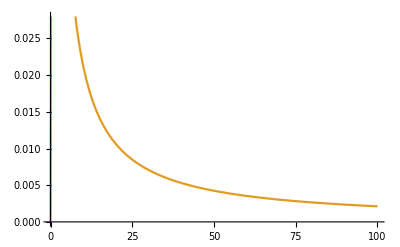

```mathematica
ListPlot[{Convergea2*0, Convergea0,Convergea01}, Joined->True]
```

```mathematica
Total[Table[a0func[2, it]/L,{it,0,100}]]
```

-5251/(20200 π)

```mathematica
(2+1 π Cot[(1  π)/2])/(2 1 π)/.it->1
```

1/π

```mathematica
Convergea0[[;;,2]]-Convergea01[[;;,2]]
```

Thread::tdlen: Objects of unequal length in {0.,0.212207,0.106103,0.0707355,0.0530516,0.0424413,0.0353678,0.0303152,0.0265258,0.0235785,«91»}+{-0.31831,-Total[Indeterminate],-0.106103,«5»,-0.0353678,-Total[Indeterminate],«90»} cannot be combined.

{-0.31831,-Total[Indeterminate],-0.106103,-Total[Indeterminate],-0.063662,-Total[Indeterminate],-0.0454728,-Total[Indeterminate],-0.0353678,-Total[Indeterminate],-0.0289373,-Total[Indeterminate],-0.0244854,-Total[Indeterminate],-0.0212207,-Total[Indeterminate],-0.0187241,-Total[Indeterminate],-0.0167532,-Total[Indeterminate],-0.0151576,-Total[Indeterminate],-0.0138396,-Total[Indeterminate],-0.0127324,-Total[Indeterminate],-0.0117893,-Total[Indeterminate],-0.0109762,-Total[Indeterminate],-0.0102681,-Total[Indeterminate],-0.00964575,-Total[Indeterminate],-0.00909457,-Total[Indeterminate],-0.00860297,-Total[Indeterminate],-0.00816179,-Total[Indeterminate],-0.00776366,-Total[Indeterminate],-0.00740256,-Total[Indeterminate],-0.00707355,-Total[Indeterminate],-0.00677255,-Total[Indeterminate],-0.00649612,-Total[Indeterminate],-0.00624137,-Total[Indeterminate],-0.00600585,-Total[Indeterminate],-0.00578745,-Total[Indeterminate],-0.00558438,-Total[Indeterminate],-0.00539508,-Total[Indeterminate],-0.00521819,-Total[Indeterminate],-0.00505254,-Total[Indeterminate],-0.00489708,-Total[Indeterminate],-0.00475089,-Total[Indeterminate],-0.00461319,-Total[Indeterminate],-0.00448324,-Total[Indeterminate],-0.00436041,-Total[Indeterminate],-0.00424413,-Total[Indeterminate],-0.00413389,-Total[Indeterminate],-0.00402924,-Total[Indeterminate],-0.00392975,-Total[Indeterminate],-0.00383506,-Total[Indeterminate],-0.00374482,-Total[Indeterminate],-0.00365873,-Total[Indeterminate],-0.00357652,-Total[Indeterminate],-0.00349791,-Total[Indeterminate],-0.00342269,-Total[Indeterminate],-0.00335063,-Total[Indeterminate],-0.00328155,-Total[Indeterminate],-0.00321525,-Total[Indeterminate]}+{0.,0.212207,0.106103,0.0707355,0.0530516,0.0424413,0.0353678,0.0303152,0.0265258,0.0235785,0.0212207,0.0192915,0.0176839,0.0163236,0.0151576,0.0141471,0.0132629,0.0124827,0.0117893,0.0111688,0.0106103,0.0101051,0.00964575,0.00922637,0.00884194,0.00848826,0.00816179,0.0078595,0.00757881,0.00731747,0.00707355,0.00684537,0.00663146,0.0064305,0.00624137,0.00606305,0.00589463,0.00573531,0.00558438,0.00544119,0.00530516,0.00517577,0.00505254,0.00493504,0.00482288,0.0047157,0.00461319,0.00451503,0.00442097,0.00433075,0.00424413,0.00416091,0.0040809,0.0040039,0.00392975,0.0038583,0.0037894,0.00372292,0.00365873,0.00359672,0.00353678,0.0034788,0.00342269,0.00336836,0.00331573,0.00326472,0.00321525,0.00316726,0.00312069,0.00307546,0.00303152,0.00298883,0.00294731,0.00290694,0.00286766,0.00282942,0.00279219,0.00275593,0.0027206,0.00268616,0.00265258,0.00261983,0.00258789,0.00255671,0.00252627,0.00249655,0.00246752,0.00243916,0.00241144,0.00238434,0.00235785,0.00233194,0.00230659,0.00228179,0.00225752,0.00223375,0.00221049,0.0021877,0.00216537,0.0021435,0.00212207}

```mathematica
a0func[1,0]
```

-(2 L)/π

2.59874-(2 L)/π

```mathematica
a0sum = 0.0;
a0sum2 = 0.0;
For[it =0, it<5000, it++; a0sum += a0func[n, it]/L;a0sum2+= -(2+it π Cot[(it π)/2])/(2 it π) ]
```

```mathematica
a0sum2
```

ComplexInfinity

```mathematica
N[-(L (2+n π Cot[(n π)/2]))/(2 n π)/.n->3]
```

-0.106103 L

-0.106103 L

```mathematica
a0sum/.n->1
```

0.318278

```mathematica
For[it =1, it<10, it++; 
Print[N[Total[Total[α2[[1;;it, 1;;it]]/L]]]]]
```

0.589531

0.431891

0.352888

0.388644

0.447675

0.421995

0.382548

0.39767

0.431215

```mathematica
Total[Total[α2]]
```

L/4+(30906666772 L)/(58605338025 π)

```mathematica
N[30906666772/(58605338025 π)]
```

0.167867

```mathematica
FullSimplify[Integrate[Cos[m π y/L]Sin[n π y/(2 L)],{y,-L,0}]]
```

(2 L (-n+n Cos[m π] Cos[(n π)/2]+2 m Sin[m π] Sin[(n π)/2]))/((-4 m^2+n^2) π)

```mathematica
∑_(m=1)^∞ (2 L (-n+n Cos[m π] Cos[(n π)/2]+2 m Sin[m π] Sin[(n π)/2]))/((-4 m^2+n^2) π)
```

1/(2 n π)(2 L-L n π Cot[(n π)/2]+L n Cos[(n π)/2] HurwitzLerchPhi[-1,1,1-n/2]-L n Cos[(n π)/2] HurwitzLerchPhi[-1,1,(2+n)/2])

```mathematica
∑_(n=1)^∞ 1/(2 n π)(2 L-L n π Cot[(n π)/2]+L n Cos[(n π)/2] HurwitzLerchPhi[-1,1,1-n/2]-L n Cos[(n π)/2] HurwitzLerchPhi[-1,1,(2+n)/2])
```

$Aborted

```mathematica
FullSimplify[Integrate[Cos[m π y/L]Sin[n π y/(2 L)],{y,-L,0}]]
```

```mathematica
(2 L (-n))/((-4 m^2+n^2) π)
```

-(2 L n)/((-4 m^2+n^2) π)

(2 L Cos[π/L] (n-n Cos[m π] Cos[(n π)/2]-2 m Sin[m π] Sin[(n π)/2]))/((4 m^2-n^2) π)

```mathematica
TeXForm[%14]
```

\frac{2 L \cos \left(\frac{\pi }{L}\right) \left(-2 m \sin (\pi  m) \sin \left(\frac{\pi 
   n}{2}\right)+n (-\cos (\pi  m)) \cos \left(\frac{\pi  n}{2}\right)+n\right)}{\pi 
   \left(4 m^2-n^2\right)}

```mathematica
FullSimplify[Integrate[Cos[m π y/L]Sin[2m π y/(2 L)]Cos[π/L],{y,-L,0}]]
```

-(L Cos[π/L] Sin[m π]^2)/(2 m π)

```mathematica
TeXForm[%16]
```

-\frac{L \cos \left(\frac{\pi }{L}\right) \sin ^2(\pi  m)}{2 \pi  m}

```mathematica
Integrate[Cos[]]
```

```mathematica
Integrate[Cos[m π y/L]Sin[n π y/(2 L)]Cos[(π  y)/L],{y,-L,0}]
```

-(2 L (n (-4-4 m^2+n^2) (1+Cos[m π] Cos[(n π)/2])+2 m (4-4 m^2+n^2) Sin[m π] Sin[(n π)/2]))/((16 m^4+(-4+n^2)^2-8 m^2 (4+n^2)) π)

```mathematica
TeXForm[%83]
```

-\frac{2 L \left(2 m \left(-4 m^2+n^2+4\right) \sin (\pi  m) \sin \left(\frac{\pi 
   n}{2}\right)+n \left(-4 m^2+n^2-4\right) \left(\cos (\pi  m) \cos \left(\frac{\pi 
   n}{2}\right)+1\right)\right)}{\pi  \left(16 m^4-8 m^2
   \left(n^2+4\right)+\left(n^2-4\right)^2\right)}

```mathematica
Solve[(16 m^4+(-4+n^2)^2-8 m^2 (4+n^2)) π==0, n]
```

{{n→-2 (-1+m)},{n→2 (-1+m)},{n→-2 (1+m)},{n→2 (1+m)}}

```mathematica
Integrate[Cos[m π y/L]Sin[2 (1+m) π y/(2 L)]Cos[(π  y)/L],{y,-L,0}]
```

-(L (1+2 m) Sin[m π]^2)/(4 m (1+m) π)

```mathematica
Integrate[Cos[2 π y/L]Sin[3 π y/(2 L)]Cos[(π  y)/L],{y,-L,0}]
```

-(22 L)/(45 π)

```mathematica
(2(3(-4*4+9-4)))/(16 2^4-8 2^2(3^2+4)+ (9-4)^2)
```

22/45

```mathematica
a1 = Integrate[Cos[m π y/L]Sin[n π/(2L)y],{y,-L,0}]
Integrate[Cos[3 π y/L]Sin[5 π y/(2 L)],{y,-L,0}]
```

(2 L (n-n Cos[m π] Cos[(n π)/2]-2 m Sin[m π] Sin[(n π)/2]))/((4 m^2-n^2) π)

(10 L)/(11 π)

```mathematica
a0func[5,3]
```

(10 L)/(11 π)

```mathematica
(2 L (n))/((4 m^2-n^2) π)
```

```mathematica
(2 L (n))/((4 m^2-n^2) π)
```

```mathematica
a1 = (2 L (n))/((4 m^2-n^2) π)
```

(2 L n)/((4 m^2-n^2) π)

```mathematica
Assuming[n ==16,∑_(m=0)^∞ a1]
```

$Aborted

```mathematica
-(L (2+n π Cot[(n π)/2]))/(2 n π)/.n->11
```

-L/(11 π)

```mathematica
-1/(2 n π)L (2+n π Cot[(n π)/2])
```

-(L (2+n π Cot[(n π)/2]))/(2 n π)

4/3+π/2

```mathematica
L n Cos[(n π)/2] HurwitzLerchPhi[-1,1,-n/2]/.n->2
```

ComplexInfinity

```mathematica
FullSimplify[1/(2 n π)(-2 L-L n π Cot[(n π)/2]-L n Cos[(n π)/2] HurwitzLerchPhi[-1,1,-n/2]+L n Cos[(n π)/2] HurwitzLerchPhi[-1,1,n/2])]
```

-(L (2+n π Cot[(n π)/2]+n Cos[(n π)/2] (HurwitzLerchPhi[-1,1,-n/2]-HurwitzLerchPhi[-1,1,n/2])))/(2 n π)

```mathematica
-1/(2 n π)L (2+n π Cot[(n π)/2])/.n->1
```

-L/π

```mathematica
Assuming[n ∈ EvenQ,  ∑_(n=1)^∞ -(L (2+n π Cot[(n π)/2]))/(2 n π)]
```

$Aborted

```mathematica
(Assuming[n ∈ EvenQ,∑)_(n=1)^∞-(L (2+n π Cot[(n π)/2]))/(2 n π)
```

```mathematica
Sum[(2 L (-n))/((-4 m^2+n^2) π),{m,0,∞}]
```

```mathematica
TeXForm[-(L (2+n π Cot[(n π)/2]))/(2 n π)]
```

-\frac{L \left(\pi  n \cot \left(\frac{\pi  n}{2}\right)+2\right)}{2 \pi  n}

```mathematica
Sum[Integrate[Cos[m π y/L]Sin[ 2 π/(2L)y],{y,-L,0}],{m,0,30}]
```

-(32 L)/(31 π)

```mathematica
1/Pi
```

1/π

```mathematica
N[1/π]
```

0.31831

```mathematica
-(L (2+n π Cot[(n π)/2]))/(2 n π)/.n->3
```

-L/(3 π)

```mathematica
d
```

```mathematica
a2 =Integrate[Cos[(m π)/L y]Cos[π/L y]Sin[(n π)/(2L)y],{y,-L,0}]
```

-(2 L (n (-4-4 m^2+n^2) (1+Cos[m π] Cos[(n π)/2])+2 m (4-4 m^2+n^2) Sin[m π] Sin[(n π)/2]))/((16 m^4+(-4+n^2)^2-8 m^2 (4+n^2)) π)

```mathematica
TrigReduce[a2]
```

(8 L n+8 L m^2 n-2 L n^3-8 L m Cos[m π-(n π)/2]+8 L m^3 Cos[m π-(n π)/2]+4 L n Cos[m π-(n π)/2]+4 L m^2 n Cos[m π-(n π)/2]-2 L m n^2 Cos[m π-(n π)/2]-L n^3 Cos[m π-(n π)/2]+8 L m Cos[m π+(n π)/2]-8 L m^3 Cos[m π+(n π)/2]+4 L n Cos[m π+(n π)/2]+4 L m^2 n Cos[m π+(n π)/2]+2 L m n^2 Cos[m π+(n π)/2]-L n^3 Cos[m π+(n π)/2])/((16-32 m^2+16 m^4-8 n^2-8 m^2 n^2+n^4) π)

```mathematica
∑_(m=1)^∞ %13
```

1/(8 π)(-2 L π Cot[(n π)/2]-2 L Cos[(n π)/2] HurwitzLerchPhi[-1,1,(4-n)/2]-2 L Cos[(n π)/2] HurwitzLerchPhi[-1,1,-n/2]+2 L Cos[(n π)/2] HurwitzLerchPhi[-1,1,n/2]+2 L Cos[(n π)/2] HurwitzLerchPhi[-1,1,(4+n)/2]-4 L n RootSum[-16 n^2+n^4-16 n^2 #1+64 #1^2-8 n^2 #1^2+64 #1^3+16 #1^4&,PolyGamma[0,-#1]/(-n^2+8 #1-n^2 #1+12 #1^2+4 #1^3)&]+L n^3 RootSum[-16 n^2+n^4-16 n^2 #1+64 #1^2-8 n^2 #1^2+64 #1^3+16 #1^4&,PolyGamma[0,-#1]/(-n^2+8 #1-n^2 #1+12 #1^2+4 #1^3)&])

```mathematica
∑_(m=0)^∞ a2
```

1/(8 π)(-2 L π Cot[(n π)/2]+2 L Cos[(n π)/2] HurwitzLerchPhi[-1,1,1/2 (-2-n)]+2 L Cos[(n π)/2] HurwitzLerchPhi[-1,1,(2-n)/2]-2 L Cos[(n π)/2] HurwitzLerchPhi[-1,1,1/2 (-2+n)]-2 L Cos[(n π)/2] HurwitzLerchPhi[-1,1,(2+n)/2]-4 L n RootSum[16-8 n^2+n^4-32 #1^2-8 n^2 #1^2+16 #1^4&,PolyGamma[0,-#1]/(-4 #1-n^2 #1+4 #1^3)&]+L n^3 RootSum[16-8 n^2+n^4-32 #1^2-8 n^2 #1^2+16 #1^4&,PolyGamma[0,-#1]/(-4 #1-n^2 #1+4 #1^3)&])

```mathematica
\
```

$Aborted

```mathematica
1/(8 π)(-2 L π Cot[(n π)/2]+-4 L n RootSum[16-8 n^2+n^4-32 #1^2-8 n^2 #1^2+16 #1^4&,PolyGamma[0,-#1]/(-4 #1-n^2 #1+4 #1^3)&]+L n^3 RootSum[16-8 n^2+n^4-32 #1^2-8 n^2 #1^2+16 #1^4&,PolyGamma[0,-#1]/(-4 #1-n^2 #1+4 #1^3)&])
```

1/(8 π)(-2 L π Cot[(n π)/2]-4 L n RootSum[16-8 n^2+n^4-32 #1^2-8 n^2 #1^2+16 #1^4&,PolyGamma[0,-#1]/(-4 #1-n^2 #1+4 #1^3)&]+L n^3 RootSum[16-8 n^2+n^4-32 #1^2-8 n^2 #1^2+16 #1^4&,PolyGamma[0,-#1]/(-4 #1-n^2 #1+4 #1^3)&])

```mathematica
%10/.n->1
```

-(3 L RootSum[9-40 #1^2+16 #1^4&,PolyGamma[0,-#1]/(-5 #1+4 #1^3)&])/(8 π)

```mathematica
1/(8 π)(-2 L π Cot[(n π)/2])
```

-1/4 L Cot[(n π)/2]

```mathematica
-(2 L (n (-4-4 m^2+n^2) (1)))/((16 m^4+(-4+n^2)^2-8 m^2 (4+n^2)) π)
```

-(2 L n (-4-4 m^2+n^2))/((16 m^4+(-4+n^2)^2-8 m^2 (4+n^2)) π)

```mathematica
∑_(m=0)^∞ -(2 L n (-4-4 m^2+n^2))/((16 m^4+(-4+n^2)^2-8 m^2 (4+n^2)) π)
```

-(L (2 n-4 π Cot[(n π)/2]+n^2 π Cot[(n π)/2]))/(2 (-2+n) (2+n) π)

```mathematica
Simplify[-(L (2 n-4 π Cot[(n π)/2]+n^2 π Cot[(n π)/2]))/(2 (-2+n) (2+n) π)]
```

```mathematica
-(L (2 n+(-4+n^2) π Cot[(n π)/2]))/(2 (-2+n) (2+n) π)/.n->4
```

ComplexInfinity

```mathematica
α1m = Table[Integrate[Cos[(m π)/L y]Cos[π/L y]Sin[(n π)/(2L)y],{y,-L,0}],{m,0,15}];
```

```mathematica
Total[α1m/.n->1]
```

(96 L)/(319 π)

```mathematica
28*3
```

84

```mathematica
96/319
```

96/319

```mathematica
N[96/319]
```

0.30094

```mathematica
TeXForm[-(L (2 n+(-4+n^2) π Cot[(n π)/2]))/(2 (-2+n) (2+n) π)]
```

-\frac{L \left(\pi  \left(n^2-4\right) \cot \left(\frac{\pi  n}{2}\right)+2 n\right)}{2
   \pi  (n-2) (n+2)}

```mathematica
a3 = Integrate[Cos[(m π)/L y]Sin[(n π)/(2L)y]Sin[π/(2L)y],{y,-L,0}]
```

(L ((2 (2 m-n) Cos[m π-(n π)/2])/(-1+(-2 m+n)^2)-(2 (2 m+n) Cos[m π+(n π)/2])/(-1+4 m^2+4 m n+n^2)))/(2 π)

```mathematica
(L ((2 (2 m-n) Cos[m π-(n π)/2])/(-1+(-2 m+n)^2)-(2 (2 m+n) Cos[m π+(n π)/2])/(-1+4 m^2+4 m n+n^2)))/(2 π)/.n->2
```

```mathematica
∑_(m=0)^∞ a3
```

1/(4 π)(L Cos[(n π)/2] HurwitzLerchPhi[-1,1,1/2 (-1-n)]+L Cos[(n π)/2] HurwitzLerchPhi[-1,1,(1-n)/2]-L Cos[(n π)/2] HurwitzLerchPhi[-1,1,1/2 (-1+n)]-L Cos[(n π)/2] HurwitzLerchPhi[-1,1,(1+n)/2])

```mathematica
Simplify[1/(4 π)(L Cos[(n π)/2] HurwitzLerchPhi[-1,1,1/2 (-1-n)]+L Cos[(n π)/2] HurwitzLerchPhi[-1,1,(1-n)/2]-L Cos[(n π)/2] HurwitzLerchPhi[-1,1,1/2 (-1+n)]-L Cos[(n π)/2] HurwitzLerchPhi[-1,1,(1+n)/2])]
```

1/(4 π)L Cos[(n π)/2] (HurwitzLerchPhi[-1,1,1/2 (-1-n)]+HurwitzLerchPhi[-1,1,(1-n)/2]-HurwitzLerchPhi[-1,1,1/2 (-1+n)]-HurwitzLerchPhi[-1,1,(1+n)/2])

```mathematica
(HurwitzLerchPhi[-1,1,1/2 (-1-n)]+HurwitzLerchPhi[-1,1,(1-n)/2]-HurwitzLerchPhi[-1,1,1/2 (-1+n)]-HurwitzLerchPhi[-1,1,(1+n)/2])/.n->6
```

-24/35

```mathematica
8*8
```

64

```mathematica
6*6
```

```mathematica
%59/.n->8
```

-(8 L)/(63 π)

```mathematica
Simplify[(-L (-2-π/2)+L (2-π/2)-L (4/3+π/2)+(L π)/2)/(4 π)]
```

(2 L)/(3 π)

```mathematica
a33 = Table[Integrate[Cos[(m π)/L y]Sin[(n π)/(2L)y]Sin[π/(2L)y],{y,0,L}],{m,0,20}];
```

```mathematica
Total[a33]
```

-(2 L n (-1601+n^2) Cos[(n π)/2])/((2556801-3202 n^2+n^4) π)+(2 L n (-1445+n^2) Cos[(n π)/2])/((2082249-2890 n^2+n^4) π)-(2 L n (-1297+n^2) Cos[(n π)/2])/((1677025-2594 n^2+n^4) π)+(2 L n (-1157+n^2) Cos[(n π)/2])/((1334025-2314 n^2+n^4) π)-(2 L n (-1025+n^2) Cos[(n π)/2])/((1046529-2050 n^2+n^4) π)+(2 L n (-901+n^2) Cos[(n π)/2])/((808201-1802 n^2+n^4) π)-(2 L n (-785+n^2) Cos[(n π)/2])/((613089-1570 n^2+n^4) π)+(2 L n (-677+n^2) Cos[(n π)/2])/((455625-1354 n^2+n^4) π)-(2 L n (-577+n^2) Cos[(n π)/2])/((330625-1154 n^2+n^4) π)+(2 L n (-485+n^2) Cos[(n π)/2])/((233289-970 n^2+n^4) π)-(2 L n (-401+n^2) Cos[(n π)/2])/((159201-802 n^2+n^4) π)+(2 L n (-325+n^2) Cos[(n π)/2])/((104329-650 n^2+n^4) π)-(2 L n (-257+n^2) Cos[(n π)/2])/((65025-514 n^2+n^4) π)+(2 L n (-197+n^2) Cos[(n π)/2])/((38025-394 n^2+n^4) π)-(2 L n (-145+n^2) Cos[(n π)/2])/((20449-290 n^2+n^4) π)+(2 L n (-101+n^2) Cos[(n π)/2])/((9801-202 n^2+n^4) π)-(2 L n (-65+n^2) Cos[(n π)/2])/((3969-130 n^2+n^4) π)+(2 L n (-37+n^2) Cos[(n π)/2])/((1225-74 n^2+n^4) π)-(2 L n (-17+n^2) Cos[(n π)/2])/((225-34 n^2+n^4) π)+(2 L n (-5+n^2) Cos[(n π)/2])/((9-10 n^2+n^4) π)+(2 L n Cos[(n π)/2])/(π-n^2 π)

```mathematica
Simplify[%61]
```

```mathematica
-(2 L n (-841+n^2) Cos[(n π)/2])/((-1681+n^2) (-1+n^2) π)/.n->8
```

```mathematica
1/(4 Pi)L Cos[8 Pi/2](4 n/(n^2-1))/.n->8
```

(8 L)/(63 π)

```mathematica
592/4851
```

592/4851

```mathematica
N[592/4851]
```

0.122037

```mathematica
8/63
```

8/63

```mathematica
N[8/63]
```

0.126984

```mathematica
868/1311
```

868/1311

```mathematica
N[868/1311]
```

0.66209

```mathematica
HurwitzLerchPhi
```

```mathematica
Table[Integrate[Cos[(m π)/L y]Sin[π/(2L)y]Cos[(n π)/L y],{y,-L,0}],{m,0,15}]
```

{(2 L (-1+2 n Sin[n π]))/(π-4 n^2 π),(2 L (3+4 n^2+2 n (-5+4 n^2) Sin[n π]))/((9-40 n^2+16 n^4) π),(2 L (15+4 n^2+(34 n-8 n^3) Sin[n π]))/((225-136 n^2+16 n^4) π),(2 L (35+4 n^2+2 n (-37+4 n^2) Sin[n π]))/((1225-296 n^2+16 n^4) π),(2 L (63+4 n^2-2 n (-65+4 n^2) Sin[n π]))/((3969-520 n^2+16 n^4) π),(2 L (99+4 n^2+2 n (-101+4 n^2) Sin[n π]))/((9801-808 n^2+16 n^4) π),(2 L (143+4 n^2+(290 n-8 n^3) Sin[n π]))/((20449-1160 n^2+16 n^4) π),(2 L (195+4 n^2+2 n (-197+4 n^2) Sin[n π]))/((38025-1576 n^2+16 n^4) π),(2 L (255+4 n^2+(514 n-8 n^3) Sin[n π]))/((65025-2056 n^2+16 n^4) π),(2 L (323+4 n^2+2 n (-325+4 n^2) Sin[n π]))/((104329-2600 n^2+16 n^4) π),(2 L (399+4 n^2+(802 n-8 n^3) Sin[n π]))/((159201-3208 n^2+16 n^4) π),(2 L (483+4 n^2+2 n (-485+4 n^2) Sin[n π]))/((233289-3880 n^2+16 n^4) π),(2 L (575+4 n^2-2 n (-577+4 n^2) Sin[n π]))/((330625-4616 n^2+16 n^4) π),(2 L (675+4 n^2+2 n (-677+4 n^2) Sin[n π]))/((455625-5416 n^2+16 n^4) π),(2 L (783+4 n^2-2 n (-785+4 n^2) Sin[n π]))/((613089-6280 n^2+16 n^4) π),(2 L (899+4 n^2+2 n (-901+4 n^2) Sin[n π]))/((808201-7208 n^2+16 n^4) π)}

```mathematica
Total[(%11 π)/L/.n->1]
```

96/319

```mathematica
N[96/319]
```

0.30094

```mathematica
N[374/1311]
```

0.285278

```mathematica
∑_(m=0)^∞ -(2 L (1-4 m^2-4 n^2))/((16 m^4+(1-4 n^2)^2-8 m^2 (1+4 n^2)) π)
```

L/((-1+4 n^2) π)

```mathematica
TeXForm[L/((-1+4 n^2) π)]
```

\frac{L}{\pi  \left(4 n^2-1\right)}

```mathematica
L/((-1+4 n^2) π)/.n->1
```

L/(3 π)

```mathematica
50/231
```

50/231

```mathematica
N[50/231]
```

0.21645

```mathematica
Cosh[2 Pi/(2L)]
```

```mathematica
Limit[Cos[n π/2]4 n^2/(n^2-1),n->1]
```

-π

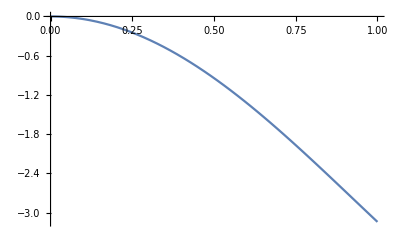

```mathematica
Plot[Cos[n π/2]4 n^2/(n^2-1),{n,0,1}]
```

```mathematica
eqs = {L TS + L An (Sinh[n π/L c0]-c1 (ρ1 κ1 -ρ2 κ2 )Cosh[n π/L c0] n/(4 n^2-1))- Bn((-ρ1 κ1 +ρ2 κ2 )(Sinh[n π/(2 L)c0](L (π n Cot[π n/2]+2))/(2 Pi n)- c1 Cosh[n π/(2L)c0]((-n (2 n+(-4+n^2) π Cot[(n π)/2]))/(4 (-2+n) (2+n))))  - c1 Cosh[n Pi/(2 L)c0](ρ1^2 κ1^2+ρ2^2 κ2^2 )1/8 Cos[n π/2](4 n^2/(n^2-1)))}
```

{L TS-Bn (-(c1 n^2 (κ1^2 ρ1^2+κ2^2 ρ2^2) Cos[(n π)/2] Cosh[(c0 n π)/(2 L)])/(2 (-1+n^2))+(-κ1 ρ1+κ2 ρ2) ((c1 n Cosh[(c0 n π)/(2 L)] (2 n+(-4+n^2) π Cot[(n π)/2]))/(4 (-2+n) (2+n))+(L (2+n π Cot[(n π)/2]) Sinh[(c0 n π)/(2 L)])/(2 n π)))+An L (-(c1 n (κ1 ρ1-κ2 ρ2) Cosh[(c0 n π)/L])/(-1+4 n^2)+Sinh[(c0 n π)/L])}

```mathematica
Limit[eqs,n->1]
```

{-1/24 Bn c1 (4 κ1 ρ1+3 π κ1^2 ρ1^2+κ2 ρ2 (-4+3 π κ2 ρ2)) Cosh[(c0 π)/(2 L)]-1/3 An c1 L (κ1 ρ1-κ2 ρ2) Cosh[(c0 π)/L]+L (TS+(Bn (κ1 ρ1-κ2 ρ2) Sinh[(c0 π)/(2 L)])/π+An Sinh[(c0 π)/L])}

{{}}

```mathematica
eqs/.Bn->0
```

{L TS+An L (-(c1 n (κ1 ρ1-κ2 ρ2) Cosh[(c0 n π)/L])/(-1+4 n^2)+Sinh[(c0 n π)/L])}

```mathematica
Solve[L TS+An L (-(c1 n (κ1 ρ1-κ2 ρ2) Cosh[(c0 n π)/L])/(-1+4 n^2)+Sinh[(c0 n π)/L])==0, An]
```

{{An→-((-1+4 n^2) TS)/(-c1 n κ1 ρ1 Cosh[(c0 n π)/L]+c1 n κ2 ρ2 Cosh[(c0 n π)/L]-Sinh[(c0 n π)/L]+4 n^2 Sinh[(c0 n π)/L])}}

```mathematica
FortranForm[-((-1+4 n^2) TS)/(-c1 n κ1 ρ1 Cosh[(c0 n π)/L]+c1 n κ2 ρ2 Cosh[(c0 n π)/L]-Sinh[(c0 n π)/L]+4 n^2 Sinh[(c0 n π)/L])]
```

-(((-1 + 4*n**2)*TS)/
     -    (-(c1*n*κ1*ρ1*Cosh((c0*n*Pi)/L)) + c1*n*κ2*ρ2*Cosh((c0*n*Pi)/L) - 
     -      Sinh((c0*n*Pi)/L) + 4*n**2*Sinh((c0*n*Pi)/L)))

```mathematica
eqs/.{Bn->An, ρ1 κ1 -> ρ2 κ2}
```

{L TS+(An c1 n^2 (κ1^2 ρ1^2+κ2^2 ρ2^2) Cos[(n π)/2] Cosh[(c0 n π)/(2 L)])/(2 (-1+n^2))+An L Sinh[(c0 n π)/L]}

```mathematica
Solve[%33[[1]] ==0, An]
```

{{An→-((2 L (-1+n^2) TS)/(c1 n^2 κ1^2 ρ1^2 Cos[(n π)/2] Cosh[(c0 n π)/(2 L)]+c1 n^2 κ2^2 ρ2^2 Cos[(n π)/2] Cosh[(c0 n π)/(2 L)]-2 L Sinh[(c0 n π)/L]+2 L n^2 Sinh[(c0 n π)/L]))}}

```mathematica
FortranForm[-((2 L (-1+n^2) TS)/(c1 n^2 κ1^2 ρ1^2 Cos[(n π)/2] Cosh[(c0 n π)/(2 L)]+c1 n^2 κ2^2 ρ2^2 Cos[(n π)/2] Cosh[(c0 n π)/(2 L)]-2 L Sinh[(c0 n π)/L]+2 L n^2 Sinh[(c0 n π)/L]))]
```

(-2*L*(-1 + n**2)*TS)/
     -  (c1*n**2*κ1**2*ρ1**2*Cos((n*Pi)/2.)*Cosh((c0*n*Pi)/(2.*L)) + 
     -    c1*n**2*κ2**2*ρ2**2*Cos((n*Pi)/2.)*Cosh((c0*n*Pi)/(2.*L)) - 
     -    2*L*Sinh((c0*n*Pi)/L) + 2*L*n**2*Sinh((c0*n*Pi)/L))

```mathematica
-((2 L (-1+n^2) TS)/(c1 n^2 κ1^2 ρ1^2 Cos[(n π)/2] Cosh[(c0 n π)/(2 L)]+c1 n^2 κ2^2 ρ2^2 Cos[(n π)/2] Cosh[(c0 n π)/(2 L)]-2 L Sinh[(c0 n π)/L]+2 L n^2 Sinh[(c0 n π)/L]))/.n->2
```

-(6 L TS)/(-4 c1 κ1^2 ρ1^2 Cosh[(c0 π)/L]-4 c1 κ2^2 ρ2^2 Cosh[(c0 π)/L]+6 L Sinh[(2 c0 π)/L])

```mathematica
-((2 L (-1+n^2) TS)/(c1 n^2 κ1^2 ρ1^2 Cos[(n π)/2] Cosh[(c0 n π)/(2 L)]+c1 n^2 κ2^2 ρ2^2 Cos[(n π)/2] Cosh[(c0 n π)/(2 L)]-2 L Sinh[(c0 n π)/L]+2 L n^2 Sinh[(c0 n π)/L]))
```

-((2 L (-1+n^2) TS)/(c1 n^2 κ1^2 ρ1^2 Cos[(n π)/2] Cosh[(c0 n π)/(2 L)]+c1 n^2 κ2^2 ρ2^2 Cos[(n π)/2] Cosh[(c0 n π)/(2 L)]-2 L Sinh[(c0 n π)/L]+2 L n^2 Sinh[(c0 n π)/L]))

```mathematica
∑_(n=1)^∞ -((2 L (-1+n^2) TS)/(c1 n^2 κ1^2 ρ1^2 Cos[(n π)/2] Cosh[(c0 n π)/(2 L)]+c1 n^2 κ2^2 ρ2^2 Cos[(n π)/2] Cosh[(c0 n π)/(2 L)]-2 L Sinh[(c0 n π)/L]+2 L n^2 Sinh[(c0 n π)/L]))
```

$Aborted

```mathematica
(An c1 n^2 (κ1^2 ρ1^2+κ2^2 ρ2^2) Cos[(n π)/2] Cosh[(c0 n π)/(2 L)])/(2 (-1+n^2))+An L Sinh[(c0 n π)/L]
```

(An c1 n^2 (κ1^2 ρ1^2+κ2^2 ρ2^2) Cos[(n π)/2] Cosh[(c0 n π)/(2 L)])/(2 (-1+n^2))+An L Sinh[(c0 n π)/L]

```mathematica
∑_(n=1)^∞ ((An c1 n^2 (κ1^2 ρ1^2+κ2^2 ρ2^2) Cos[(n π)/2] Cosh[(c0 n π)/(2 L)])/(2 (-1+n^2))+An L Sinh[(c0 n π)/L])
```

∑_(n=1)^∞ ((An c1 n^2 (κ1^2 ρ1^2+κ2^2 ρ2^2) Cos[(n π)/2] Cosh[(c0 n π)/(2 L)])/(2 (-1+n^2))+An L Sinh[(c0 n π)/L])

```mathematica
n^2/(2 (-1+n^2))
```

n^2/(2 (-1+n^2))

```mathematica
∑_(n=1)^∞ n^2/(2 (-1+n^2))
```

Power::infy: Infinite expression 1/0 encountered.

```mathematica
∑_(n=2)^∞ n^2/(2 (-1+n^2))
```

Sum::div: Sum does not converge.

```mathematica
∑_(n=2)^∞ (n^2 Cos[(n π)/2] Cosh[(c0 n π)/(2 L)]/Sinh[(c0 n π)/L]^2)/(2 (-1+n^2))+∑_(n=1)^∞ Sinh[(c0 n π)/L]/Cosh[(c0 n π)/L]
```

```mathematica
∑_(n=1)^∞ (n^2 Cos[(n π)/2] Cosh[(c0 n π)/(2 L)]/Sinh[(c0 n π)/L]^2)/(2 (-1+n^2)n)
```

$Aborted

```mathematica
(n^2 Cos[(n π)/2] Cosh[(c0 n π)/(2 L)]/Sinh[(c0 n π)/L]^2)/(2 (-1+n^2)n)
```

(n Cos[(n π)/2] Cosh[(c0 n π)/(2 L)] Csch[(c0 n π)/L]^2)/(2 (-1+n^2))

```mathematica
Simplify[(n Cos[(n π)/2] Cosh[(c0 n π)/(2 L)] Csch[(c0 n π)/L]^2)/(2 (-1+n^2))]
```

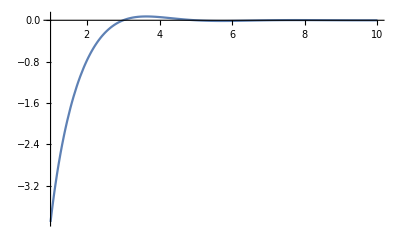

```mathematica
Plot[(n Cos[(n π)/2] Cosh[(c0 n π)/(2 L)] Csch[(c0 n π)/L]^2)/(-2+2 n^2)/.{L->1, c0->.1},{n,1,10}, PlotRange->All]
```

```mathematica
(n Cos[(n π)/2] Cosh[(c0 n π)/(2 L)] Csch[(c0 n π)/L]^2)/(-2+2 n^2)/.n->2 + (n Cos[(n π)/2] Cosh[(c0 n π)/(2 L)] Csch[(c0 n π)/L]^2)/(-2+2 n^2)/.n->4 + (n Cos[(n π)/2] Cosh[(c0 n π)/(2 L)] Csch[(c0 n π)/L]^2)/(-2+2 n^2)/.n->6
```

```mathematica
Simplify[%76]/.{L->1, c0->.1}
```

-0.689311

```mathematica
(n Cos[(n π)/2] Cosh[(c0 n π)/(2 L)] Csch[(c0 n π)/L]^2)/(-2+2 n^2)/.n->4
```

2/15 Cosh[(2 c0 π)/L] Csch[(4 c0 π)/L]^2

```mathematica
(n Cos[(n π)/2] Cosh[(c0 n π)/(2 L)] Csch[(c0 n π)/L]^2)/(-2+2 n^2)/.n->6
```

-3/35 Cosh[(3 c0 π)/L] Csch[(6 c0 π)/L]^2

```mathematica
Sum[Sinh[(c0 n π)/L]/Sinh[(c0 n π)/L]^2/n,{n,1,∞,2}]
```

Sum[Csch[(c0 n π)/L]/n,{n,1,∞,2}]

```mathematica
(-QPolyGamma[0,1,ⅇ^((c0 π)/L)]+QPolyGamma[0,1-(ⅈ π)/Log[ⅇ^((c0 π)/L)],ⅇ^((c0 π)/L)])/Log[ⅇ^((c0 π)/L)]
```

```mathematica
(-QPolyGamma[0,1,ⅇ^((c0 π)/L)]+QPolyGamma[0,1-(ⅈ π)/Log[ⅇ^((c0 π)/L)],ⅇ^((c0 π)/L)])/.{L->1, c0->.1}
```

2.42959-3.14159 ⅈ

```mathematica
Simplify[%45]
```

1/16 ⅇ^(-(c0 π)/(2 L)) (1-ⅈ ⅇ^((c0 π)/(2 L))) (-ⅈ+ⅇ^((c0 π)/(2 L))) (Log[1-ⅈ ⅇ^(-(c0 π)/(2 L))]-Log[1+ⅈ ⅇ^(-(c0 π)/(2 L))]+Log[1-ⅈ ⅇ^((c0 π)/(2 L))]-Log[1+ⅈ ⅇ^((c0 π)/(2 L))])

```mathematica
Re[%46]
```

1/16 Re[ⅇ^(-(c0 π)/(2 L)) (1-ⅈ ⅇ^((c0 π)/(2 L))) (-ⅈ+ⅇ^((c0 π)/(2 L))) (Log[1-ⅈ ⅇ^(-(c0 π)/(2 L))]-Log[1+ⅈ ⅇ^(-(c0 π)/(2 L))]+Log[1-ⅈ ⅇ^((c0 π)/(2 L))]-Log[1+ⅈ ⅇ^((c0 π)/(2 L))])]

```mathematica
N[Log[1-ⅈ ⅇ^(-(c0 π)/(2 L))]/.{L->1, c0->.1}]
```

0.274177-0.707179 ⅈ

```mathematica
ⅇ^(-(c0 π)/(2 L)) (1-ⅈ ⅇ^((c0 π)/(2 L))) (-ⅈ+ⅇ^((c0 π)/(2 L))) (Log[1-ⅈ ⅇ^(-(c0 π)/(2 L))]-Log[1+ⅈ ⅇ^(-(c0 π)/(2 L))]+Log[1-ⅈ ⅇ^((c0 π)/(2 L))]-Log[1+ⅈ ⅇ^((c0 π)/(2 L))])/.{L->1, c0->.1}
```

-6.36086+0. ⅈ